{Binding Energy cs, bs, cc, bc, bb}

-0.0241966

-0.0304985

-0.0762821

-0.0988409

-0.125162

{Ωcc 1/2+}

{3.72622,4.4918,{3.0733,2.93887,2.45721,2.04279}}

{0.476329}

{{0.326557},{0.309312}}

{Ωcc^* 3/2+}

{3.81978,4.68787,{3.07613,2.94663,2.46931,2.04279}}

{0.495473}

{{0.124279},{0.117716}}

{Ωbb 1/2+}

{10.4075,3.83076,{3.06169,2.90772,2.41369,2.04279}}

{0.450288}

{{0.0277619},{0.0262958}}

{Ωbb^* 3/2+}

{10.4506,3.96583,{3.06437,2.9148,2.42294,2.04279}}

{0.465461}

{{-0.282592},{-0.267669}}

{Ωccc 3/2+}

{4.84085,4.22195,{3.06899,2.92717,2.43997,2.04279}}

{0.680807}

{{0.548888},{0.519902}}

{Ωccb 1/2+}

{8.11311,3.74602,{3.05991,2.90305,2.40778,2.04279}}

{0.4399}

{{0.249121},{0.235965}}

{Ωccb^* 3/2+}

{8.13449,3.83294,{3.06173,2.90783,2.41384,2.04279}}

{0.449074}

{{0.327053},{0.309781}}

{Ωcbb 1/2+}

{11.3744,3.18342,{3.04578,2.867,2.36651,2.04279}}

{0.111806}

{{-0.100043},{-0.0947597}}

{Ωcbb^* 3/2+}

{11.4033,3.3142,{3.04948,2.87626,2.37644,2.04279}}

{0.114289}

{{0.109745},{0.103949}}

{Ωbbb 3/2+}

{14.6255,2.58861,{3.02443,2.81595,2.31865,2.04279}}

{0.283617}

{{-0.0949944},{-0.0899778}}

{Mass Spectrum}

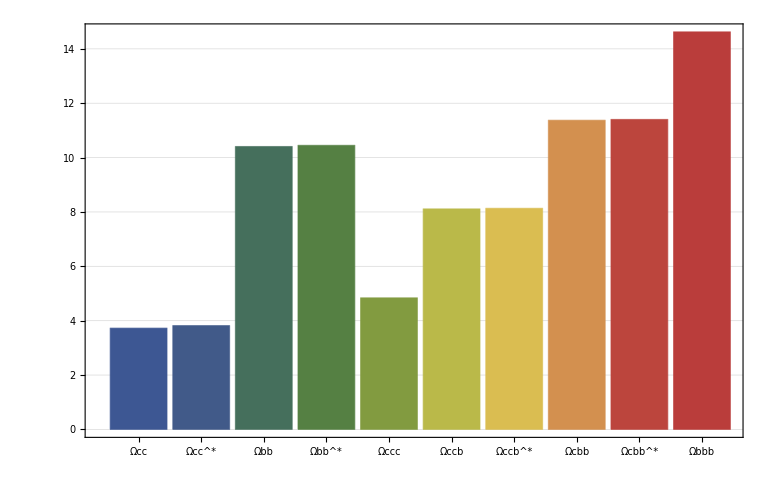

{Charge Radius}

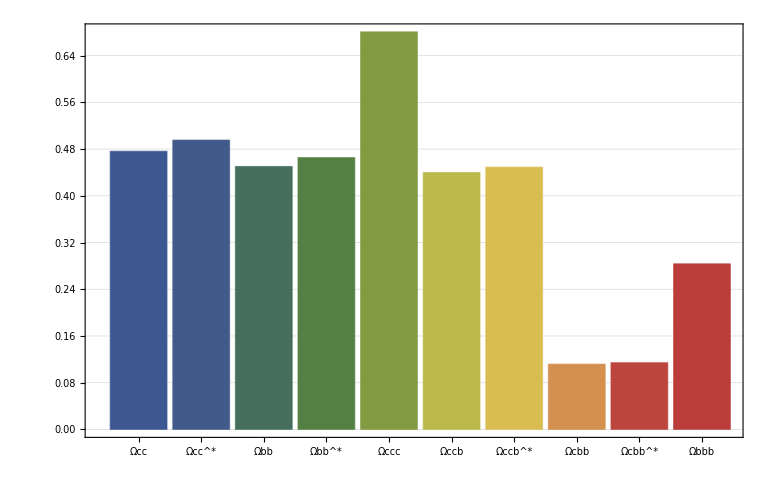

{Magnetic Moment}

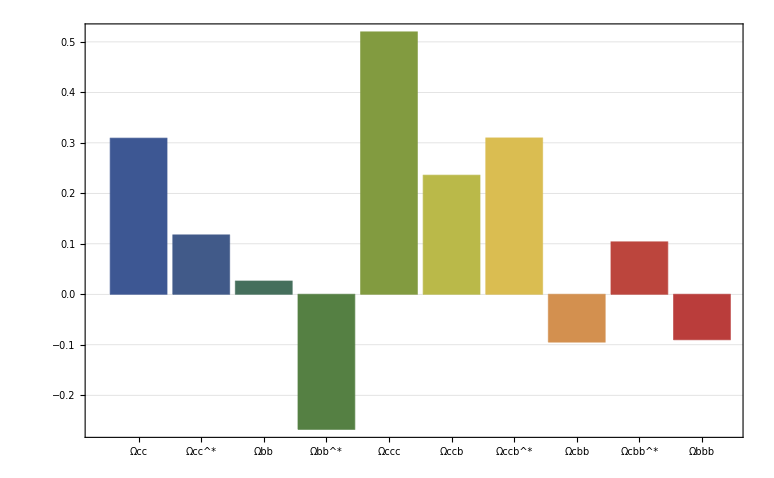

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.275)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ωcc 1/2+"}
Ωcc=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,32/3,0},{0,0,0,0},{0,0,0,0}},2Bcs+Bcc]
rΩcc=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},Ωcc];
μΩcc=MagneticMoment[{0,4/3,-1/3,0,0},{0,0,0,0,0},Ωcc];
{rΩcc}
{{μΩcc},{μΩcc/μNp}}

{"Ωcc^* 3/2+"}
SuperStar[Ωcc]=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs+Bcc]
SuperStar[rΩcc]=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},SuperStar[Ωcc]];
SuperStar[μΩcc]=MagneticMoment[{0,2,1,0,0},{0,0,0,0,0},SuperStar[Ωcc]];
{SuperStar[rΩcc]}
{{SuperStar[μΩcc]},{SuperStar[μΩcc]/μNp}}

{"Ωbb 1/2+"}
Ωbb=Hadron[{2,0,1,0},{{-8/3,0,32/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs+Bbb]
rΩbb=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},Ωbb];
μΩbb=MagneticMoment[{4/3,0,-1/3,0,0},{0,0,0,0,0},Ωbb];
{rΩbb}
{{μΩbb},{μΩbb/μNp}}

{"Ωbb^* 3/2+"}
SuperStar[Ωbb]=Hadron[{2,0,1,0},{{-8/3,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs+Bbb]
SuperStar[rΩbb]=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},SuperStar[Ωbb]];
SuperStar[μΩbb]=MagneticMoment[{2,0,1,0,0},{0,0,0,0,0},SuperStar[Ωbb]];
{SuperStar[rΩbb]}
{{SuperStar[μΩbb]},{SuperStar[μΩbb]/μNp}}

{"Ωccc 3/2+"}
Ωccc=Hadron[{0,3,0,0},{{0,0,0,0},{0,-8,0,0},{0,0,0,0},{0,0,0,0}},3Bcc]
rΩccc=ChargeRadius[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
μΩccc=MagneticMoment[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
{rΩccc}
{{μΩccc},{μΩccc/μNp}}

{"Ωccb 1/2+"}
Ωccb=Hadron[{1,2,0,0},{{0,32/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bcc]
rΩccb=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},Ωccb];
μΩccb=MagneticMoment[{-1/3,4/3,0,0,0},{0,0,0,0,0},Ωccb];
{rΩccb}
{{μΩccb},{μΩccb/μNp}}

{"Ωccb^* 3/2+"}
SuperStar[Ωccb]=Hadron[{1,2,0,0},{{0,-16/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bcc]
SuperStar[rΩccb]=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},SuperStar[Ωccb]];
SuperStar[μΩccb]=MagneticMoment[{1,2,0,0,0},{0,0,0,0,0},SuperStar[Ωccb]];
{SuperStar[rΩccb]}
{{SuperStar[μΩccb]},{SuperStar[μΩccb]/μNp}}

{"Ωcbb 1/2+"}
Ωcbb=Hadron[{2,1,0,0},{{-8/3,32/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bbb]
rΩcbb=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},Ωcbb];
μΩcbb=MagneticMoment[{4/3,-1/3,0,0,0},{0,0,0,0,0},Ωcbb];
{rΩcbb}
{{μΩcbb},{μΩcbb/μNp}}

{"Ωcbb^* 3/2+"}
SuperStar[Ωcbb]=Hadron[{2,1,0,0},{{-8/3,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bbb]
SuperStar[rΩcbb]=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},SuperStar[Ωcbb]];
SuperStar[μΩcbb]=MagneticMoment[{2,1,0,0,0},{0,0,0,0,0},SuperStar[Ωcbb]];
{SuperStar[rΩcbb]}
{{SuperStar[μΩcbb]},{SuperStar[μΩcbb]/μNp}}

{"Ωbbb 3/2+"}
Ωbbb=Hadron[{3,0,0,0},{{-8,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},3Bbb]
rΩbbb=ChargeRadius[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
μΩbbb=MagneticMoment[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
{rΩbbb}
{{μΩbbb},{μΩbbb/μNp}}

{"Mass Spectrum"}
BarChart[{First[Ωcc],First[SuperStar[Ωcc]],First[Ωbb],First[SuperStar[Ωbb]],First[Ωccc],First[Ωccb],First[SuperStar[Ωccb]],First[Ωcbb],First[SuperStar[Ωcbb]],First[Ωbbb]},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩcc,SuperStar[rΩcc],rΩbb,SuperStar[rΩbb],rΩccc,rΩccb,SuperStar[rΩccb],rΩcbb,SuperStar[rΩcbb],rΩbbb},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩcc/μNp,SuperStar[μΩcc]/μNp,μΩbb/μNp,SuperStar[μΩbb]/μNp,μΩccc/μNp,μΩccb/μNp,SuperStar[μΩccb]/μNp,μΩcbb/μNp,SuperStar[μΩcbb]/μNp,μΩbbb/μNp},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```